# Reorganization energy for a redox molecule near metal electrode covered with dielectric

## Units

```mathematica
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189`10*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
```

## Parameters

Dielectric permittivities:
solvent statis: ϵ_s
solvent optical: ϵ_∞
SAM: ϵ_m
metal electrode: ∞

```mathematica
ϵs=78;
ϵinf=1.78;
ϵm=2.25;
```

## Liu-Newton spherical model [Y.-P. Liu, M. Newton, J. Phys. Chem. 1994, 98, 7162-7169]

```mathematica
η21=(ϵm-ϵs)/(ϵm+ϵs)
```

-0.943925

```mathematica
η21inf=(ϵm-ϵinf)/(ϵm+ϵinf)
```

0.116625

```mathematica
Clear[λ]
```

λ [R, L, Acc→acc] - Reorganization energy (kcal/mol):
R - radius of the spherical cavity around the redox molecule (Å);
L - thickness of the SAM (Å);
(R+L) - distance from the center of spherical cavity to the electrode surface (Å);
dq - absolute change in total charge in a.u. (number of electrons transferred);
acc - series convergence criterion (default is 10^-10 Hartrees);

```mathematica
λ[R_,L_,dq_,OptionsPattern[{Acc->10^-10}]]:=Module[{eps,r,l,η21,η21inf,a0,asum,aprev,diff,n},
eps=OptionValue[Acc];
r=R a2bohr;
l=L a2bohr;
η21=(ϵm-ϵs)/(ϵm+ϵs);
η21inf=(ϵm-ϵinf)/(ϵm+ϵinf);
asum=0;
aprev=0;
diff=10^10;
n=1;
a0=(1/ϵinf-1/ϵs)1/(2r)-(η21inf/ϵinf-η21/ϵs)1/(4r);
While[diff>eps,aprev=asum;asum+=((ϵm*η21inf^(n-1))/(ϵinf+ϵm)^2-(ϵm*η21^(n-1))/(ϵm+ϵs)^2)(-1)^n/(r+n*l);diff=Abs[asum-aprev];n++];
dq^2(a0+asum)au2kcal];
```

```mathematica
λ[5.0,10.0,1]
```

14.1011

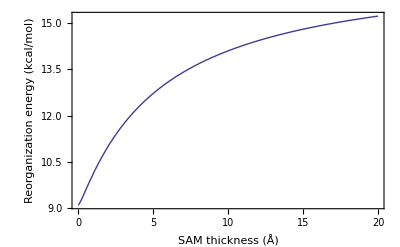

```mathematica
Plot[λ[5,d,1],{d,0,20},Axes->False,Frame->True,FrameLabel->{"SAM thickness (Å)","Reorganization energy (kcal/mol)"}]
```

```mathematica
λλ[R_,L_,δ_,dq_,OptionsPattern[{Acc->10^-10}]]:=Module[{eps,r,l,η21,η21inf,a0,asum,aprev,diff,n},
eps=OptionValue[Acc];
δ=δ a2bohr;
r=R a2bohr;
l=L a2bohr;
η21=(ϵm-ϵs)/(ϵm+ϵs);
η21inf=(ϵm-ϵinf)/(ϵm+ϵinf);
asum=0;
aprev=0;
diff=10^10;
n=1;
a0=(1/ϵinf-1/ϵs)1/(2r)-(η21inf/ϵinf-η21/ϵs)1/(4(l-δ));
While[diff>eps,aprev=asum;asum+=((ϵm*η21inf^(n-1))/(ϵinf+ϵm)^2-(ϵm*η21^(n-1))/(ϵm+ϵs)^2)(-1)^n/((l-δ)+n*δ);diff=Abs[asum-aprev];n++];
dq^2(a0+asum)au2kcal];
```

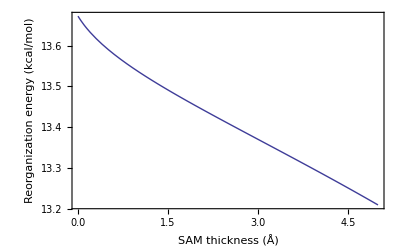

```mathematica
Plot[λλ[5,10,δ,1],{δ,0,5},Axes->False,Frame->True,FrameLabel->{"SAM thickness (Å)","Reorganization energy (kcal/mol)"}]
```